#### A two-host, environmental-transmission model

This model assumes environmental transmission, but where the parasite actively seeks out hosts. Contact is thus controlled by the parasite (so β_i can quantify both the contact and infection processes), and contact is assumed to remove parasites from the environment. I will assume that the resident parasite strain exploits a single host and ask whether a mutant that can exploit both hosts can invade if “generalism” comes at a cost of reducing the shedding rate from both hosts. Let the parameter a quantify the cost of generalism. I will let K_1 and K_2 be the carrying capacities of the first host and second host; similarly, μ_1 and μ_2 will be the mortality rates of hosts 1 and 2 and λ_1 and λ_2 will be the shedding rates from hosts 1 and 2. For simplicity, I will assume that all other parameters (traits) are equal between the hosts and parasites.

```mathematica
dS1dt=r (S1+I1r+I1m) (1-(S1+I1r+I1m)/K1)-β S1 (Pr+Pm);
dS2dt=r (S2+I2m) (1-(S2+I2m)/K2)-β S2 (Pr+Pm);dI1rdt=β S1 Pr-μ1 I1r;
dPrdt=λ1 I1r-β S1 Pr-γ Pr;
dI1mdt=β S1 Pm-μ1 I1m;
dI2mdt=β S2 Pm-μ2 I2m;
dPmdt=a λ1 I1m+a λ2 I2m-β S1 Pm-β S2 Pm-γ Pm;
```

For an invasion analysis, we assume that the resident parasite comes to an ecological equilibrium with the host. Since it does not parasitize the second host, it will go to its carrying capacity: S_2=K_2. The density of the exploited host at equilibrium will be S_1=(γ μ_1)/(β (λ_1-μ_1)).

```mathematica
Eq=Solve[({dS1dt==0,dI1rdt==0,dPrdt==0}/.{I1m->0,Pm->0}),{S1,I1r,Pr}];
Eq[[1;;4,1]]
```

{S1→0,S1→K1,S1→-(γ μ1)/(β (-λ1+μ1)),S1→-(γ μ1)/(β (-λ1+μ1))}

While evaluating the stability of the endemic equilibrium is somewhat challenging, it is obvious that, for there to be any chance for the endemic parasite equilibrium to be stable, the parasite extinction equilibrium must be unstable. This requires (λ_1 β K)/(μ (β K+γ))>1 or, equivalently, (β K (λ_1-μ))/(γ μ)>1. Notice that this second expression for the condition is the reciprocal of the equilibrium host abundance at the endemic equilibrium, which is as expected.

```mathematica
Jres={{D[dS1dt,S1],D[dS1dt,I1r],D[dS1dt,Pr]},
{D[dI1rdt,S1],D[dI1rdt,I1r],D[dI1rdt,Pr]},
{D[dPrdt,S1],D[dPrdt,I1r],D[dPrdt,Pr]}}/.{I1m->0,Pm->0};
Simplify[Eigenvalues[Jres/.Eq[[2]]]]
```

{-r,1/2 (-K1 β-γ-μ1-√((K1 β+γ+μ1)^2-4 (γ μ1+K1 β (-λ+μ1)))),1/2 (-K1 β-γ-μ1+√((K1 β+γ+μ1)^2-4 (γ μ1+K1 β (-λ+μ1))))}

We can calculate the invasion criterion from the rows and columns of the Jacobian dealing with the mutant parasite alone:

```mathematica
J={{D[dS1dt,S1],D[dS1dt,S2],D[dS1dt,I1r],D[dS1dt,Pr],D[dS1dt,I1m],D[dS1dt,I2m],D[dS1dt,Pm]},
{D[dS2dt,S1],D[dS2dt,S2],D[dS2dt,I1r],D[dS2dt,Pr],D[dS2dt,I1m],D[dS2dt,I2m],D[dS2dt,Pm]},
{D[dI1rdt,S1],D[dI1rdt,S2],D[dI1rdt,I1r],D[dI1rdt,Pr],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,Pm]},
{D[dPrdt,S1],D[dPrdt,S2],D[dPrdt,I1r],D[dPrdt,Pr],D[dPrdt,I1m],D[dPrdt,I2m],D[dPrdt,Pm]},
{D[dI1mdt,S1],D[dI1mdt,S2],D[dI1mdt,I1r],D[dI1mdt,Pr],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,Pm]},
{D[dI2mdt,S1],D[dI2mdt,S2],D[dI2mdt,I1r],D[dI2mdt,Pr],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,Pm]},
{D[dPmdt,S1],D[dPmdt,S2],D[dPmdt,I1r],D[dPmdt,Pr],D[dPmdt,I1m],D[dPmdt,I2m],D[dPmdt,Pm]}}/.{I1m->0,I2m->0,Pm->0};
MatrixForm[J]
(* The eigenvalues of this matrix determine whether the mutant parasite can invade *)
MatrixForm[J[[5;;7,5;;7]]]
```

(-(r (I1r+S1))/K1+r (1-(I1r+S1)/K1)-Pr β | 0 | -(r (I1r+S1))/K1+r (1-(I1r+S1)/K1) | -S1 β | -(r (I1r+S1))/K1+r (1-(I1r+S1)/K1) | 0 | -S1 β
0 | -(r S2)/K2+r (1-S2/K2)-Pr β | 0 | -S2 β | 0 | -(r S2)/K2+r (1-S2/K2) | -S2 β
Pr β | 0 | -μ1 | S1 β | 0 | 0 | 0
-Pr β | 0 | λ | -S1 β-γ | 0 | 0 | 0
0 | 0 | 0 | 0 | -μ1 | 0 | S1 β
0 | 0 | 0 | 0 | 0 | -μ2 | S2 β
0 | 0 | 0 | 0 | a λ1 | a λ2 | -S1 β-S2 β-γ)

(-μ1 | 0 | S1 β
0 | -μ2 | S2 β
a λ1 | a λ2 | -S1 β-S2 β-γ)

Rather than look at those eigenvalues (which are difficult to interpret), it is easier to apply the next generation theorem.

```mathematica
F={{0,0,S1 β},{0,0,S2 β},{a λ1,a λ2,0}};
V={{μ1,0,0},{0,μ2,0},{0,0,S1 β+S2 β+γ}};
Simplify[Dot[F,Inverse[V]]];
Eigenvalues[Dot[F,Inverse[V]]]
```

{0,-(√a √β √(S2 λ2 μ1+S1 λ1 μ2))/(√(S1 β+S2 β+γ) √μ1 √μ2),(√a √β √(S2 λ2 μ1+S1 λ1 μ2))/(√(S1 β+S2 β+γ) √μ1 √μ2)}

Invasion requires 
(a λ β (μ_1 S_2+μ_2 S_1))/(μ_1 μ_2(β S_1+β S_2+γ))>1, which is equivalent to requiring that (β (a λ_1-μ_1))/(γ μ_1)S_1+(β (a λ_1-μ_2))/(γ μ_2)S_2>1.

```mathematica
a β λ (S2 μ1+S1 μ2)>(S1 β+S2 β+γ) μ1 μ2;
a S2 β λ μ1+a S1 β λ μ2>S1 β μ1 μ2+S2 β μ1 μ2+γ μ1 μ2;
β S2 μ1 (a λ-μ2)+β S1 μ2 (a λ-μ1)>γ μ1 μ2;
(β (a λ-μ1))/(γ μ1)S1+(β (a λ-μ2))/(γ μ2)S2>1;
```

Define invasion fitness as:

```mathematica
InvFit=((β (a λ1-μ1))/(γ μ1)S1+(β (a λ2-μ2))/(γ μ2)S2)/.{Eq[[3,1]],S2->K2}
```

-(a λ1-μ1)/(-λ1+μ1)+(K2 β (a λ2-μ2))/(γ μ2)

Notice that both a λ_1-μ_1>0 and a λ_2-μ_2>0 for invasion to be possible. This is because, by assumption, a λ_1-μ_1>a λ_2-μ_2. If a λ_1-μ_1<0, then invasion fitness is obviously negative. If a λ_1-μ_1>0 but a λ_2-μ_2<0, invasion fitness will be less than 1: (a λ_1-μ_1)/(λ_1-μ_1)<1 because a<1, so if the second term of invasion fitness is negative, the entire expression must be less than one.

What is the effect of increasing a on the invasion fitness?

```mathematica
D[InvFit,a]
```

-λ/(-λ+μ1)+(K2 β λ)/(γ μ2)

What is the effect of increasing K_2 on the invasion fitness?

```mathematica
D[InvFit,K2]
```

(β (a λ-μ2))/(γ μ2)

What is the effect of increasing μ on the invasion fitness?

```mathematica
Simplify[D[InvFit,μ1]]
Simplify[D[InvFit,μ2]]
```

((-1+a) λ)/(λ-μ1)^2

-(a K2 β λ)/(γ μ2^2)

What is the effect of increasing γ on the invasion fitness?

```mathematica
D[InvFit,γ]
```

-(K2 β (a λ-μ2))/(γ^2 μ2)

#### Effect of body size

We can incorporate body size of the two hosts into the model in a fairly simple way. In particular, assume that carrying capacity and mortality rate scale with body size and temperature according to 
K=K_0 e^(E/k T)W^-0.75
μ = μ_0 e^(-E/k T)W^-0.25
Notice that this form implies that mortality rate increases as temperature increases and decreases as mass increases, whereas carrying capacity decreases with both an increase in temperature and an increase in mass. This will be important later.

However, because within-host (or on-host, for ectoparasites) abundance also correlates with body size in an allometric way. If we assume that shedding rate is a linear function of abundance, we have a third allometric scaling. 
λ = λ_0 e^(-E/k T)W^0.75 (for endoparasites)
λ = λ_0 e^(-E/k T)W^(5/12) (for ectoparasites)

```mathematica
InvFitW=-(a λ1[W]-μ1[W])/(-λ1[W]+μ1[W])+(K2[W] β (a λ2[W]-μ2[W]))/(γ μ2[W]);
```

Given the definition of μ_1(W), the derivative of the first term of the invasion fitness expression can be written as

```mathematica
μ1=Q2 Exp[-Ε/(k T)] W^(-1/4);
λ1=Q3 Exp[-Ε/(k T)] W^(3/4);
D[μ1,W]==-μ1/(4 W)//Simplify
D[λ1,W]==(3 λ1)/(4 W)//Simplify
Clear[μ1,λ1]
Simplify[D[(a λ1[W]-μ1[W])/(λ1[W]-μ1[W]),W]/.{μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W)}]
```

True

True

-((-1+a) λ1[W] μ1[W])/(W (λ1[W]-μ1[W])^2)

The derivative of the second term of the invasion fitness expression with respect to mass W can be expressed as

```mathematica
K2=Q1 Exp[Ε/(k T)] (f W)^(-3/4);
μ2=Q2 Exp[-Ε/(k T)] (f W)^(-1/4);
λ2=Q3 Exp[-Ε/(k T)] (f W)^(3/4);
D[K2,W]==(-3 K2)/(4 W)//Simplify
D[μ2,W]==-μ2/(4 W)//Simplify
D[λ2,W]==(3 λ2)/(4 W)//Simplify
Clear[μ2,K2,λ2]
D[(K2[W] β (a λ2[W]-μ2[W]))/(γ μ2[W]),W]/.{K2'[W]->(-3 K2[W])/(4 W),μ2'[W]->(-μ2[W])/(4 W),λ2'[W]->(3 λ2[W])/(4 W)}//Simplify
```

True

True

True

(β K2[W] (a λ2[W]+3 μ2[W]))/(4 W γ μ2[W])

Thus, we can rewrite the derivative of invasion fitness with respect to size as:

```mathematica
(D[InvFitW,W]/.{μ1'[W]->(-μ1[W])/(4 W),μ2'[W]->(-μ2[W])/(4 W),K2'[W]->(-3 K2[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W),λ2'[W]->(3 λ2[W])/(4 W)})==((1-a) λ1[W] μ1[W])/(W (λ1[W]-μ1[W])^2)+(β K2[W] (a λ2[W]+3 μ2[W]))/(4 W γ μ2[W])//Simplify
```

True

Notice that because f occurs only in the second term of invasion fitness (dealing with infection in the secondary host), it is clear that the derivative of invasion fitness with respect to f must also be positive.

```mathematica
InvFitf=-(a λ1[W]-μ1[W])/(-λ1[W]+μ1[W])+(K2[f] β (a λ2[f]-μ2[f]))/(γ μ2[f]);
Simplify[D[InvFitf,f]/.{μ2'[f]->(-μ2[f])/(4 f),K2'[f]->(-3 K2[f])/(4 f),λ2'[f]->(3 λ2[f])/(4 f)}]
```

(β K2[f] (a λ2[f]+3 μ2[f]))/(4 f γ μ2[f])

With respect to temperature, the first term actually has a derivative of zero because both λ and μ scale with temperature in the same way. That is, both shedding rate and mortality rate increase at the same magnitude with an increase in temperature.

```mathematica
μ1=Q2 Exp[-Ε/(k T)] W^(-1/4);
λ1=Q3 Exp[-Ε/(k T)] W^(3/4);
D[μ1,T]==Ε/(k T^2)μ1//Simplify
D[λ1,T]==Ε/(k T^2)λ1//Simplify
Clear[μ1,λ1]
Simplify[D[(a λ1[T]-μ1[T])/(λ1[T]-μ1[T]),T]/.{μ1'[T]->Ε/(k T^2)μ1[T],λ1'[T]->Ε/(k T^2)λ1[T]}]
```

True

True

0

The second term is guaranteed to decrease with any increase in temperature.

```mathematica
K2=Q1 Exp[Ε/(k T)] (f W)^(-3/4);
D[K2,T]==-Ε/(k T^2)K2//Simplify
Clear[K2]
D[(K2[T] β (a λ2[T]-μ2[T]))/(γ μ2[T]),T]/.{K2'[T]->-Ε/(k T^2)K2[T],μ2'[T]->Ε/(k T^2)μ2[T],λ2'[T]->Ε/(k T^2)λ2[T]}//Simplify
```

True

(β Ε K2[T] (-a λ2[T]+μ2[T]))/(k T^2 γ μ2[T])

We can also look at the derivative of invasion fitness as both mass and temperature increase. This is negative, meaning that

```mathematica
D[(K2[W,T] β (a λ2[W,T]-μ2[W,T]))/(γ μ2[W,T]),W,T]/.{Derivative[0,1][K2][W,T]->-Ε/(k T^2)K2[W,T],Derivative[0,1][μ2][W,T]->Ε/(k T^2)μ2[W,T],Derivative[0,1][λ2][W,T]->Ε/(k T^2)λ2[W,T],
Derivative[1,0][μ2][W,T]->(-μ2[W,T])/(4 W),Derivative[1,0][K2][W,T]->(-3 K2[W,T])/(4 W),Derivative[1,0][λ2][W,T]->(3 λ2[W,T])/(4 W),Derivative[1,1][K2][W,T]->Ε/(k T^2)(3 K2[W,T])/(4 W),Derivative[1,1][μ2][W,T]->-Ε/(k T^2)μ2[W,T]/(4 W),Derivative[1,1][λ2][W,T]->Ε/(k T^2)(3 λ2[W,T])/(4 W)}//Simplify
```

```mathematica
-(β Ε K2[W,T] (a λ2[W,T]+3 μ2[W,T]))/(4 k T^2 W γ μ2[W,T])
InvFit
```

-(β Ε K2[W,T] (a λ2[W,T]+3 μ2[W,T]))/(4 k T^2 W γ μ2[W,T])

InvFit

```mathematica
μ1=Q2 Exp[-Ε/(k T)] W^(-1/4);
λ1=Q3 Exp[-Ε/(k T)] W^(3/4);
μ2=Q2 Exp[-Ε/(1.1 k T)] (1.1 W)^(-1/4);
λ2=Q3 Exp[-Ε/(1.1 k T)] (1.1 W)^(3/4);
(* First term of R0 expression *)
(* If you increase W and temperature by 10% does the magnitude of this term increase or decrease *)
Expand[Numerator[Simplify[((a λ1-μ1)/(λ1-μ1))/((a λ2-μ2)/(λ2-μ2))]]]
Expand[Denominator[Simplify[((a λ1-μ1)/(λ1-μ1))/((a λ2-μ2)/(λ2-μ2))]]]
```

1. Q2^2-1.1 Q2 Q3 W-1. a Q2 Q3 W+1.1 a Q3^2 W^2

1. Q2^2-1. Q2 Q3 W-1.1 a Q2 Q3 W+1.1 a Q3^2 W^2

Assuming both the numerator and denominator are positive (which is necessary for invasion to be possible at all), the entire expression is less than one (meaning that increasing both mass and temperature has increased the magnitude of the first term of invasion fitness) when
1. Q2^2-1.1 Q2 Q3 W-1. a Q2 Q3 W+1.1 a Q3^2 W^2<1. Q2^2-1. Q2 Q3 W-1.1 a Q2 Q3 W+1.1 a Q3^2 W^2
0.1 a Q2 Q3 W<0.1 Q2 Q3 W
a < 1
which is always true. Thus, increasing mass has a positive effect on R_0 that offsets the negative effect of increasing temperature.

```mathematica
(* Second term of invasion fitness *)
Clear[μ2,λ2]
Simplify[((K2 β (a λ2-μ2))/(γ μ2))/((K3 β (a λ3-μ3))/(γ μ3))/.{μ2->Q2 Exp[-Ε/(k T)] W^(-1/4),λ2->Q3 Exp[-Ε/(k T)] W^(3/4),K2->Q1 Exp[Ε/(k T)] W^(-3/4)}/.{μ3->Q2 Exp[-Ε/(1.1 k T)] (1.1 W)^(-1/4),λ3->Q3 Exp[-Ε/(1.1 k T)] (1.1 W)^(3/4),K3->Q1 Exp[Ε/(1.1 k T)] (1.1 W)^(-3/4)}]
```

(1.0741 ⅇ^((0.0909091 Ε)/(k T)) (Q2-1. a Q3 W))/(1. Q2-1.1 a Q3 W)

Both the numerator and denominator should be positive, but which should be larger in magnitude? If the denominator is larger, than increasing

```mathematica
a K2 λ2 μ3-K2 μ2 μ3<a K3 λ3 μ2-K3 μ2 μ3;
```

(a K2 λ2+K3 μ2) μ3<μ2 (a K3 λ3+K2 μ3)

Notice that (Q_2-1.1 Q_3 W)/(Q_2-Q_3 W)>1 requires Q_2-1.1 Q_3 W>Q_2-Q_3 W (assuming Q_2-Q_3 W >0), which would imply that (after rearranging) 0.1 Q_3<0, which is impossible. If Q_2-Q_3 W<0, then this requires Q_2-1.1 Q_3 W<Q_2-Q_3 W, or 0.1W>0, which is always true. Similarly, if Q
If Q_2-Q_3 W>0, then Q_2-1.1 Q_3 W>0 as well, and (Q_2-1.1 Q_3 W)/(Q_2-Q_3 W)<1.
If Q_2-a Q_3 W>0, then Q_2-1.1 a Q_3 W>0 as well, and (Q_2-a Q_3 W)/(Q_2-1.1 a Q_3 W)>1.

```mathematica
(1. (1. Q2-1.1 Q3 W) (Q2-1. a Q3 W))/((Q2-1. Q3 W) (1. Q2-1.1 a Q3 W))
(* Notice that (Subscript[Q, 2]-1.1 Subscript[Q, 3] W)>
```

```mathematica
(K2[f] β (a λ2[f]-μ2[f]))/(γ μ2[f])
```

#### Numerics

```mathematica
allom={μ1[W]->Q2 Exp[-Ε/(k T)] W^(-1/4),K1[W]->Q1 Exp[Ε/(k T)] W^(-3/4),μ2[W]->Q2 Exp[-Ε/(k T)] (f W)^(-1/4),K2[W]->Q1 Exp[Ε/(k T)] (f W)^(-3/4)}/.{Q1->2.984 10^-9,Q2->1.785 10^8,Ε->0.43,k->8.617 10^-5,T->270}
```

{μ1[W]→1.67886/W^(1/4),K1[W]→0.317265/W^(3/4),μ2[W]→1.67886/(f W)^(1/4),K2[W]→0.317265/(f W)^(3/4)}

```mathematica
Simplify[D[(β K1[W] (λ-μ1[W]))/(γ μ1[W]),W]/.{μ1'[W]->(-μ1[W])/(4 W),K1'[W]->(-3 K1[W])/(4 W)}]
```

-(β K1[W] (2 λ-3 μ1[W]))/(4 W γ μ1[W])

```mathematica
(β K1[W] (λ-μ1[W]))/(γ μ1[W])/.allom
```

(0.188977 β (-1.67886/W^(1/4)+λ))/(√W γ)

```mathematica
(λ-μ1[W]/.allom/.λ->2)
```

```mathematica
?Table
```

$Aborted

```mathematica
?Plot
```

RowBox[{"Plot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a plot of StyleBox["f", "TI"] as a function of StyleBox["x", "TI"] from SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]] to SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"Plot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several functions SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Plot", "[", RowBox[{StyleBox["…", "TR"], ",", RowBox[{RowBox[{"{", StyleBox["x", "TI"], "}"}], "∈", StyleBox["reg", "TI"]}]}], "]"}] takes the variable StyleBox["x", "TI"] to be in the geometric region StyleBox["reg", "TI"].

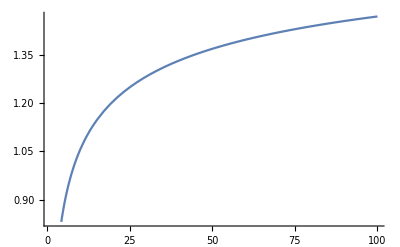

```mathematica
Plot[2-1.6788596711945776/W^(1/4), {W, 1, 100}]
```

```mathematica
allom
```

{μ1[W]→1.67886/W^(1/4),K1[W]→0.317265/W^(3/4),μ2[W]→1.67886/(f W)^(1/4),K2[W]→0.317265/(f W)^(3/4)}

```mathematica
InvFitW/.allom
(* This must be positive for persistence of the resident *)
(β K1[W] (λ-μ1[W]))/(γ μ1[W])/.allom
```

{μ1[W]→1.67886/W^(1/4),K1[W]→0.317265/W^(3/4),μ2[W]→1.67886/(f W)^(1/4),K2[W]→0.317265/(f W)^(3/4)}

r

(0.188977 β (-1.67886/W^(1/4)+λ))/(√W γ)

### Trophic transmission model

Let D_1 and D_2 be two definitive hosts and N be prey of both and intermediate host.

```mathematica
dNsdt=s Ns-a1 D1 Ns-a2 D2 Ns-β Ns (Pr+Pm);
dD1sdt=r (D1+I1r+I1m) (1-(S1+I1r+I1m)/K1)-b1 D1 Ni;
dD2sdt=r (D2+I2m) (1-(S2+I2m)/K2)-β S2 (Pr+Pm);

dNirdt=β Ns Pr-a1 D1 Nir-a2 D2 Nir;
dNimdt=β Ns Pm-a1 D1 Nim-a2 D2 Nim;

dD1irdt=a1 D1 Nir-μ1 D1ir;
dD1imdt=a1 D1 Nim-μ1 D1im;
dD2imdt=a2 D2 Nim-μ2 D2im;

dPrdt=λ1 I1r-β S1 Pr-γ Pr;
dPmdt=a λ1 I1m+a λ2 I2m-β S1 Pm-β S2 Pm-γ Pm;
```